# h=√12 QR=1/(√12)(I+C+C^2)(1+D+D^2+D^3)

Norm extrapolation for the paper
“COMPUTATIONAL EXPLORATIONS OF THE THOMPSON GROUP T FOR THE AMENABILITY PROBLEM OF F” 
by S. Haagerup, U. Haagerup, M. Ramirez-Solano:

```mathematica
norms={{1,2.},{2,2.449489742783178},{3,2.715194527703128},{4,2.8284271247461903},{5,2.9223966828183867},{6,2.972659289346513},{7,3.016533946476901},{8,3.042347938092436},{9,3.068417764643332},{10,3.08578329683099},{11,3.103092357020246},{12,3.114538105311276},{13,3.126652934037856},{14,3.135336519301216},{15,3.144583598323395},{16,3.1512114784688667},{17,3.1584117543440793},{18,3.163730522316822},{19,3.169560293127732},{20,3.173936903387868},{21,3.178798794684903},{22,3.182493488730315},{23,3.186604857260527},{24,3.1897649630216507},{25,3.1933163691676536},{26,3.1960699911867922},{27,3.1991698413520857},{28,3.2016021109335737}}
Ntuple=Length[norms]
Mnorm=norms[[#]][[2]]&;
```

{{1,2.},{2,2.44949},{3,2.71519},{4,2.82843},{5,2.9224},{6,2.97266},{7,3.01653},{8,3.04235},{9,3.06842},{10,3.08578},{11,3.10309},{12,3.11454},{13,3.12665},{14,3.13534},{15,3.14458},{16,3.15121},{17,3.15841},{18,3.16373},{19,3.16956},{20,3.17394},{21,3.1788},{22,3.18249},{23,3.1866},{24,3.18976},{25,3.19332},{26,3.19607},{27,3.19917},{28,3.2016}}

28

```mathematica
Table[{i,Mnorm[i]^2},{i,1,Ntuple}]
```

{{1,4.},{2,6.},{3,7.37228},{4,8.},{5,8.5404},{6,8.8367},{7,9.09948},{8,9.25588},{9,9.41519},{10,9.52206},{11,9.62918},{12,9.70035},{13,9.77596},{14,9.83034},{15,9.88841},{16,9.93013},{17,9.97556},{18,10.0092},{19,10.0461},{20,10.0739},{21,10.1048},{22,10.1283},{23,10.1545},{24,10.1746},{25,10.1973},{26,10.2149},{27,10.2347},{28,10.2503}}

```mathematica
Table[{i,Mnorm[i]^2},{i,1,Ntuple}]//MatrixForm
```

(1 | 4.
2 | 6.
3 | 7.37228
4 | 8.
5 | 8.5404
6 | 8.8367
7 | 9.09948
8 | 9.25588
9 | 9.41519
10 | 9.52206
11 | 9.62918
12 | 9.70035
13 | 9.77596
14 | 9.83034
15 | 9.88841
16 | 9.93013
17 | 9.97556
18 | 10.0092
19 | 10.0461
20 | 10.0739
21 | 10.1048
22 | 10.1283
23 | 10.1545
24 | 10.1746
25 | 10.1973
26 | 10.2149
27 | 10.2347
28 | 10.2503)

```mathematica
myFit=Function[{a,d},Module[{b,c,ori,model,fit,res1,res2,diff,var,},
(*Clear[aa,b,cc,d];*)
(*d=0;*)
ori=Table[{i,Mnorm[i]^2},{i,1,Ntuple}];
(*aa=11.66*)
model=a-b ((x-d )^(-c));
fit=FindFit[ori[[Range[Length[ori]-10,Length[ori]]]],model,{b,c},x];
res1=Table[model/.fit,{x,1,Ntuple,1}];
res2=Table[Mnorm[i]^2,{i,1,Ntuple,1}];
diff=Drop[(res1-res2)^2,1];
var=Total[diff]/(Ntuple-1);
(*Print["V= ",variance," fit(a,b,c,d)= ",{a,b,c,d}/.fit];*)
{var,{a,b,c,d}/.fit}
]]
modelf=Function[args,Module[{a,b,c,d},{a,b,c,d}=args;a-b ((x-d )^(-c))]]
modelff=Function[args,Module[{a,b,c,d},{a,b,c,d}=args;a-b ((#-d )^(-c))&]]
plot=Function[f,ListPlot[Table[{x,f[x]},{x,0.01,Ntuple,.01}],PlotStyle->{Red,PointSize[.002]}]];
```

Function[{a,d},Module[{b,c,ori,model,fit,res1,res2,diff,var,Null},ori=Table[{i,Mnorm[i]^2},{i,1,Ntuple}];model=a-b (x-d)^-c;fit=FindFit[ori⟦Range[Length[ori]-10,Length[ori]]⟧,model,{b,c},x];res1=Table[model/.fit,{x,1,Ntuple,1}];res2=Table[Mnorm[i]^2,{i,1,Ntuple,1}];diff=Drop[(res1-res2)^2,1];var=Total[diff]/(Ntuple-1);{var,{a,b,c,d}/.fit}]]

Function[args,Module[{a,b,c,d},{a,b,c,d}=args;a-b (x-d)^-c]]

Function[args,Module[{a,b,c,d},{a,b,c,d}=args;a-b (#1-d)^-c&]]

```mathematica
fits=Flatten[Table[myFit[aa,d],{aa,9.89,11.66,.1},{d,-1,1,.2}],1];
xxxByExtrapolatedNorm=Table[fits⟦i⟧⟦2⟧⟦1⟧,{i,1,Length[fits]}];
fits=fits[[Ordering[xxxByExtrapolatedNorm]]];
ori=Table[{i,Mnorm[i]^2},{i,1,Ntuple}];
pics=Table[Show[ListPlot[ori,PlotLabel->ToString[i]<>":"<>ToString[fits⟦i⟧],PlotRange->{0,16}],plot[modelff[fits⟦i,2⟧]]],{i,1,Length[fits]}];
```

Power::infy: Infinite expression 1/0.^17.3123 encountered.

Power::infy: Infinite expression 1/0.^15.1846 encountered.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^5.43276 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^17.5772 encountered.

Power::infy: Infinite expression 1/0.^17.3123 encountered.

Power::infy: Infinite expression 1/0.^15.4288 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
(*Sorted by extrapolated norm*)
Manipulate[pics[[i]],{i,1,Length[pics],1}]
```

```mathematica
good 103,104,117,130
excellent 91
superexcellent 89,90
Chosen
```

10.69-13.5844/(0.8+x)^1.0201

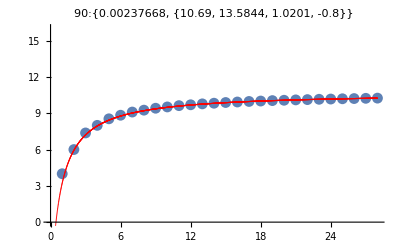

```mathematica
modelf[fits⟦90⟧⟦2⟧]
pics⟦90⟧
```

```mathematica
fitsV=Flatten[Table[myFit[aa,d],{aa,9.89,11.66,.1},{d,-1,1,.2}],1];
xxxByVariance=Table[fitsV⟦i⟧⟦1⟧,{i,1,Length[fitsV]}];
fitsV=fitsV[[Ordering[xxxByVariance]]];
oriV=Table[{i,Mnorm[i]^2},{i,1,Ntuple}];
picsV=Table[Show[ListPlot[oriV,AspectRatio->1,PlotLabel->ToString[i]<>":"<>ToString[fitsV⟦i⟧],PlotRange->{0,16},ImageSize->{800,800},PlotStyle->{PointSize[.01]}],plot[modelff[fitsV⟦i,2⟧]]],{i,1,Length[fitsV]}];
```

Power::infy: Infinite expression 1/0.^17.3123 encountered.

Power::infy: Infinite expression 1/0.^15.1846 encountered.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^5.43276 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^0.614677 encountered.

Power::infy: Infinite expression 1/0.^0.544922 encountered.

Power::infy: Infinite expression 1/0.^0.608921 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
(*Sorted by variance*)
Manipulate[picsV[[i]],{i,1,Length[pics],1},ContentSize->{900,900}]
```

good 4
excellent 5
superexcellent1, 2,3
Chosen 3

10.79-8.95223/(0.2+x)^0.840986

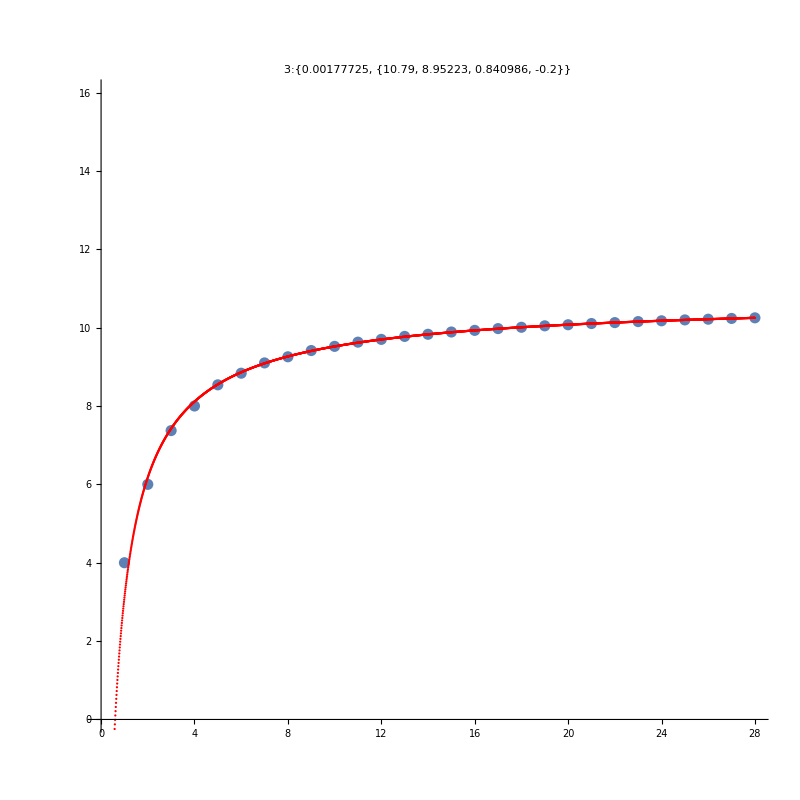

```mathematica
modelf[fitsV⟦3⟧⟦2⟧]
picsV⟦3⟧
```

```mathematica
Sqrt[10.790000000000001]
```

3.28481

```mathematica
(*Run .nb program that computes norms. But run first Clear[Mnorm]*)
```

Part::partd: Part specification List ⟦ 2 ⟧ is longer than depth of object.

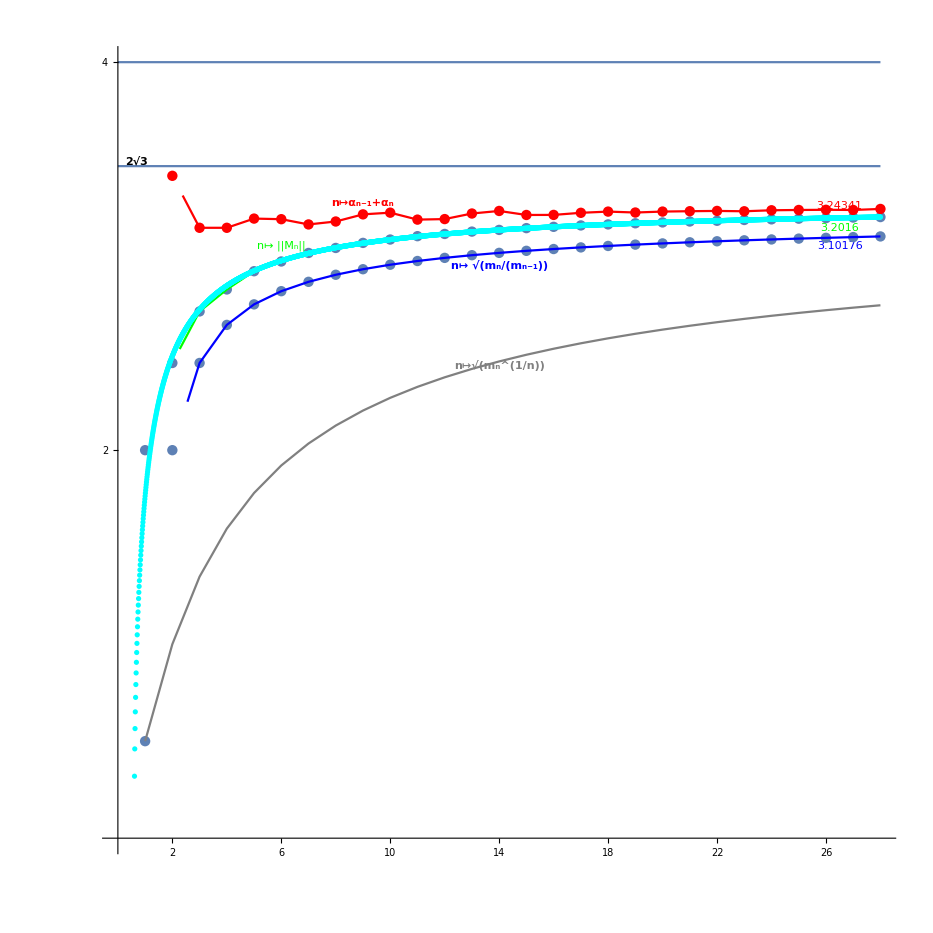

```mathematica
ma[0]=1;
Table[ma[i]=m⟦i⟧,{i,1,Length[m]}];
Show[
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Ticks->{Range[2,Ntuple,2]},PlotStyle->{PointSize[.008]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{0,4},AspectRatio->1],
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Joined->True,PlotStyle->{Green}],
Graphics[{Green,Text[Style[HoldForm["n↦ ||M_n||"],Large],{6,.08+Mnorm[6]}]}],
Graphics[{Green,Text[Style[Mnorm[Ntuple],Large],{Ntuple-1.5,-.055+Mnorm[Ntuple]}]}],
Graphics[{Red,Text[Style[N[α[Ntuple-1]+α[Ntuple]],Large],{Ntuple-1.5,.015+α[Ntuple-1]+α[Ntuple]}]}],
Graphics[{Blue,Text[Style[N[(ma[Ntuple]/ma[Ntuple-1])^(1/2)],Large],{Ntuple-1.5,-.05+(ma[Ntuple]/ma[Ntuple-1])^(1/2)}]}],
Plot[8,{x,0,Ntuple}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotStyle->{PointSize[.008]}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Blue,PointSize[.008]}],
Graphics[{Blue,Text[Style[HoldForm[n↦(Subscript[m, n]/Subscript[m, n-1])^(1/2)],Large,Bold],{14,-.065+(ma[14]/ma[13])^(1/2)}]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple}],PlotStyle->{Red,PointSize[.008]},Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Red}],
Graphics[{Red,Text[Style[HoldForm[n↦Subscript[α, n-1]+Subscript[α, n]],Large,Bold],{10-1,.05+α[9]+α[10]}]}],
ListPlot[Table[{i,(ma[i]^(1/i))^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Gray}],
Graphics[{Gray,Text[Style[HoldForm[n↦√((Subscript[m, n])^(1/n))],Large,Bold],{14,-.02+(ma[14]^(1/(2 14)))}]}],
Graphics[{Black,Text[Style[HoldForm["2√3"],Medium,Bold],{.7,2 Sqrt[3]+.025}]}],
ListPlot[Table[{x,Sqrt[10.790000000000001-8.952234982146173/(0.19999999999999996+x)^0.8409864358969407]},{x,0.01,28,.01}],PlotStyle->{PointSize[.004],Dotted,Cyan}],
Plot[Sqrt[12],{x,0,Ntuple}],

Plot[4,{x,0,Ntuple}]

]
```